```mathematica
zmin = 60
```

60

```mathematica
zmax = 200
```

200

```mathematica
200
r0 = 1
```

200

1

```mathematica
risk[z_, r_] = (1 - (z - zmin) ^ 2 / (r * (zmax - zmin)) ^ 2)
```

1-(-60+z)^2/(19600 r^2)

```mathematica
sq[z_] = zmin ^ 2  / z ^ 2
```

3600/z^2

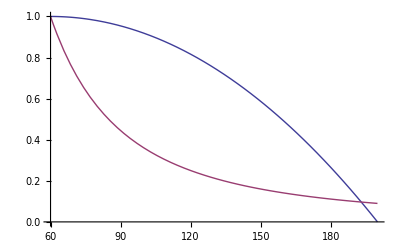

```mathematica
Plot[{risk[z, 1],sq[z]},{z,zmin,zmax}]
```

```mathematica
Plot3D[risk[z,r],{z,zmin,zmax},{r,0,1}, PlotRange->{0, 1}]
```

-Graphics3D-

```mathematica
Plot3D[risk[z,r] - sq[z],{z,zmin,zmax},{r,0,1}, PlotRange->{0, 1}]
```

-Graphics3D-

```mathematica
data = ReadList["~/Documents/Projects/rover/data/all.txt", {Number, Number, Number}];
```

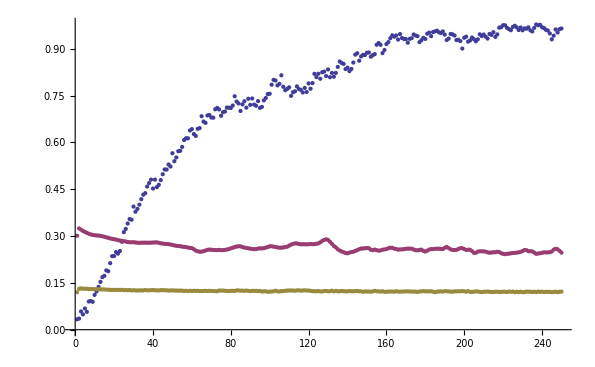

```mathematica
ListPlot[{data[[All, 1]], data[[All, 2]], data[[All, 3]]}]
```